```mathematica
U - napeti [Volt]
I - proud [Amper]
R - odpor [Ohm]
```

```mathematica
ClearAll["Global`*"]

uzel1=iUz[t]+iR1[t] == 0;
uzel2 = iR1[t] == iC1[t] + iR2[t];
uzel3 = iR2[t] == iC2[t] + iR3[t];

zdroj = u1[t] == uZ[t];

rez1= u1[t] - u2[t] == iR1[t] * R1;
rez2 =u2[t] - u3[t]== iR1[t] * R2;
rez3 =u3[t] == iR3[t] * R3;

kond1 = iC1[t]==C1*u2'[t];
kond2 = iC2[t]==C2*u3'[t];
pocpodm1 = u2[0] == 0;
pocpodm2 = u3[0] == 0;

rovnice = {uzel1, uzel2, uzel3, zdroj, rez1, rez2, rez3, kond1, kond2, pocpodm1, pocpodm2}
nezname = {u1[t], u2[t], u3[t], iR1[t], iR2[t], iR3[t], iC1[t], iC2[t], iUz[t]}

soucastky = {R1-> 10000,R2->10*10^3,R3->1*10^6,C1->33*10^-9, C2->22*10^-9};

frekvence = 917;
perioda = 1/frekvence;
tmax = 5*perioda;
amplituda = 3.3;
uZ[t_] := amplituda* (1 + Tanh[100 * Sin[2*π*frekvence*t]]) / 2;

Plot[uZ[t],{t,0,tmax}];

reseni = NDSolve[rovnice /. soucastky, nezname, {t, 0, tmax} ]

Plot[{u1[t]/. reseni, u2[t]/. reseni, u3[t]/. reseni}, {t,0,tmax}, PlotStyle->{Yellow, Green,Blue }, AxesLabel->{"t[s]", "U[V]"}]
```

{iR1[t]+iUz[t]==0,iR1[t]==iC1[t]+iR2[t],iR2[t]==iC2[t]+iR3[t],u1[t]==uZ[t],u1[t]-u2[t]==R1 iR1[t],u2[t]-u3[t]==R2 iR1[t],u3[t]==R3 iR3[t],iC1[t]==C1 u2'[t],iC2[t]==C2 u3'[t],u2[0]==0,u3[0]==0}

{u1[t],u2[t],u3[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],iUz[t]}

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

-Graphics-

{0==iC1[t]+iUz[t],iC1[t]==iR1[t],iC1[t]==C1 (u1'[t]-u2'[t]),R1 iR1[t]==u2[t],uZ[t]==u1[t],u1[0]==0,u2[0]==0}

{iUz[t],iC1[t],iR1[t],u1[t],u2[t]}

{R1→47000,C1→1/1000000000}

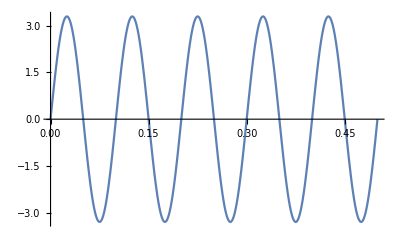

{{iUz[t]→InterpolatingFunction[…][t],iC1[t]→InterpolatingFunction[…][t],iR1[t]→InterpolatingFunction[…][t],u1[t]→InterpolatingFunction[…][t],u2[t]→InterpolatingFunction[…][t]}}

```mathematica
ClearAll["Global`*"]
rovnice = {
uzel1= 0 ==iUz[t]+iC1[t],
uzel2 = iC1[t]== iR1[t],
kond1 = iC1[t] == C1 *(u1'[t]-u2'[t]),
rez1=R1*iR1[t]==u2[t],
zdroj = uZ[t]==u1[t],
pp1 = u1[0]==0,
pp2 = u2[0]==0
}

nezname = {iUz[t], iC1[t], iR1[t], u1[t], u2[t]}
soucastky = {R1 -> 47*10^3, C1 -> 1*10^-9}

frekvence = 10;
perioda = 1 / frekvence;
tmax = 5*perioda;
amplituda = 3.3;
uZ[t_] := amplituda*Sin[2*π*frekvence*t]

Plot[uZ[t], {t,0,tmax}];

reseni = NDSolve[rovnice /. soucastky, nezname, {t, 0, tmax}, Method->{"IndexReduction" -> Automatic}, StartingStepSize-> 10^-9]
```

```mathematica
ClearAll["Global`*"]

rovnice = {
uzel1= 0 ==iUz[t]+iL1[t],
uzel2 = iL1[t]== iR1[t],
civka = u1[t] - u2[t] == L1*iL1'[t],
rez1=R1*iR1[t]==u2[t],
zdroj = uZ[t]==u1[t],
pp1 = iL1[0]==0
}

nezname = {iUz[t], iL1[t], iR1[t], u1[t], u2[t]}
soucastky = {R1 -> 47*10^3, L1 -> 1*10^-9}

frekvence = 100;
perioda = 1 / frekvence;
tmax = 5*perioda;
amplituda = 3.3;
uZ[t_] := amplituda*Sin[2*π*frekvence*t];

Plot[uZ[t], {t,0,tmax}];

reseni = NDSolve[rovnice /.soucastky, nezname, {t,0,tmax}, Method->{"IndexReduction" -> Automatic}, StartingStepSize-> 10^-9];

Plot[{u1[t]} /.reseni[[1]], u2[t] /. reseni[[2]], {t,0,tmax}]
```

{0==iL1[t]+iUz[t],iL1[t]==iR1[t],u1[t]-u2[t]==L1 iL1'[t],R1 iR1[t]==u2[t],uZ[t]==u1[t],iL1[0]==0}

{iUz[t],iL1[t],iR1[t],u1[t],u2[t]}

{R1→47000,L1→1/1000000000}

Plot::nonopt: Options expected (instead of {t,0,tmax}) beyond position 2 in Plot[{u1[t]}/.reseni⟦1⟧,u2[t]/.reseni⟦2⟧,{t,0,tmax}]. An option must be a rule or a list of rules.

Plot[{u1[t]}/.reseni⟦1⟧,u2[t]/.reseni⟦2⟧,{t,0,tmax}]